# Dünne Linsen

## Funktionen

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Abbildungsgleichung(Laplace)

```mathematica
fLaplace[vg_,dvg_,vb_,dvb_]:=Module[{g,b,db,dg,f,fe},
f=1/(1/g+1/b);
fe = GError[f,{g,b},{dg,db}];
{f,fe}/.{g->vg,b->vb,dg->dvg,db->dvb}]
```

### Bessel

```mathematica
fBessel[va_,dva_,ve_,dve_] := Module[{a,e,da,de,f,fe},
f=1/4((a^2-e^2)/a);
fe= GError[f,{a,e},{da,de}];
{f,fe}/.{a->va,e->ve,da->dva,de->dve}]
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

## Laplace

### Berechnung

```mathematica
b = {{904, 815, 780, 740, 728, 765, 753, 759, 818, 899}} 10^-3;
db=1 10^-3;

h = {{351, 380, 400, 420, 460, 470, 500, 510, 600, 700}} 10^-3;
dh = 1 10^-3;

g = {{151, 151, 151, 151, 151, 151, 151, 151, 151, 151}} 10^-3;
dg=1 10^-3;

f = fLaplace[g[[1]],dg,b[[1]],db];Grid[f//N,Frame->All]
{Mean[f[[1]]],StandardDeviation[f[[1]]]/(√Length[b[[1]]])}//N
```

0.129388 | 0.127396 | 0.126509 | 0.12541 | 0.12506 | 0.126108 | 0.125778 | 0.125944 | 0.12747 | 0.129285
0.000754715 | 0.000736239 | 0.00072823 | 0.000718497 | 0.000715449 | 0.000724655 | 0.000721731 | 0.0007232 | 0.000736905 | 0.000753743

{0.126835,0.000482622}

### Graph

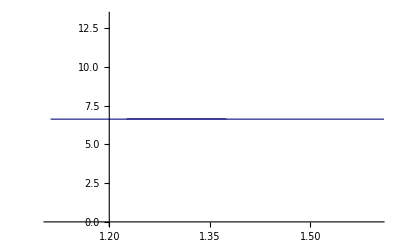

```mathematica
ListLinePlot[Table[{1/b[[1,x]],1/g[[1,x]]},{x,1,Length[b[[1]]]}]]
```

## Bessel Verfahren

### Messung

```mathematica
g2 = {150,150,150,150,150} 10^-3;
B2 = {816,783,618,604,552} 10^-3;
H22 = {344,349,375,366,371} 10^-3;
H12 = {816,783,618,604,552} 10^-3;
d2=10^-3;

a2= g2+B2//N;
da2=2 10^-3;
e2= -H22+H12+g2;
de2=2 10^-3;
f2=Grid[fBessel[a2,da2,e2,de2],Frame->All]
{Mean[f2[[1,1]]],StandardDeviation[f2[[1,1]]]}
```

0.141375 | 0.141863 | 0.141724 | 0.138585 | 0.136483
0.00135119 | 0.00132184 | 0.00114265 | 0.00114699 | 0.00108267

{0.140006,0.00238258}

## Zerstreuungslinse

### Methode 1 : ohne/mit Zerstreuung

bo3 ist Abstand von der Sammellinse zum Bild ohne Zerstreuungslinse
bm3 ist der Abstand von der Sammellinse zum Bild mit Zerstreuungslinse
lsz3 ist der Abstand der Linsen
gsz3 ist der Gegenstandsabstand für die Zerstreuungslinse

```mathematica
bo3= {922,922,922,922,922,817,817,817,817,817}10^-3;
dbo3=5 10^-3;

bm3={1829,1094,973,955,1549,1943,1520,875,1220,990} 10^-3;
dbm3=15 10^-3;

ls3 = {780,780,780,780,780,600,600,600,600,600}10^-3;
dls3 = 10^-3;

lz3 = {800,830,865,890,805,690,700,760,710,730}10^-3;
dlz3=10^-3;

lsz3=lz3-ls3//N;
dlsz3=dlz3+dls3;

gz3 =bo3-lsz3
dgz3 = dbo3+dlsz3;

bz3 = bm3 -lsz3;
dbz3 = dbm3+dlsz3;

f3 = fLaplace[-gz3,dgz3,bz3,dbz3] //N//MatrixForm
```

{0.902,0.872,0.837,0.812,0.897,0.727,0.717,0.657,0.707,0.687}

(-1.79903 | -5.29284 | -14.5736 | -20.7921 | -2.18027 | -1.19639 | -1.44828 | -8.09922 | -1.94732 | -3.41514
0.0446589 | 0.694838 | 6.70107 | 14.8825 | 0.076149 | 0.0260438 | 0.0462442 | 3.24513 | 0.105426 | 0.441066)

### Methode 2 : Bildpunkt der Sammellinse in den Brennpunkt der Zerstreuungslinse legen

lsz4 Abstand Sammellinse zu Zerstreuungslinse
bo4 Abstand Bild ohne Zerstreungslinse

```mathematica
lsz4 = 1;
dlsz4 = 0.1;

bo4 = 3;
dbo4 = 0.1;

f4 = bo4 - lsz4;
df4 = dbo4+lsz4;
{f4,df4}
```

{2,1.1}